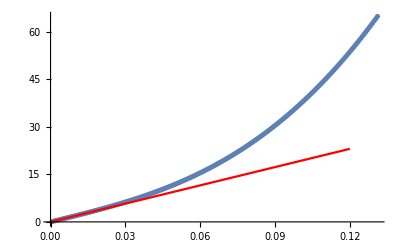

```mathematica
SetDirectory[NotebookDirectory[]];
ClearAll[WKSol];
<<"data/WKSol.mx"
Show[ListPlot[WKSol],
Plot[192x,{x,0,0.12},PlotStyle->Red]]
```

```mathematica
BendTests=Import["data/201708_BendTests_FF_processed_data_Info.mat","MAT"];
Bendlabels=Import["data/201708_BendTests_FF_processed_data_Info.mat","Labels"]
```

{Bstif,D,E,Fstar,K_s,Kc_SE,Kcant,L,N_L,SSpattern,evbool,indx_fail,sD,s_L,w0star,w_sstar}

```mathematica
BendTestAll=Import["data/201708_BendTests_FF_processed_data_Fw0.mat"];
BendlabelAll=Import["data/201708_BendTests_FF_processed_data_Fw0.mat","Labels"]
```

{Len,dflctn,force,w0star}

```mathematica
force= BendTestAll[[Position[BendlabelAll,"force"][[1,1]] ]];
dflctn= BendTestAll[[Position[BendlabelAll,"dflctn"][[1,1]] ]];
w0star= BendTestAll[[Position[BendlabelAll,"w0star"][[1,1]] ]];
Len= BendTestAll[[Position[BendlabelAll,"Len"][[1,1]] ]];
```

```mathematica
StartInd [n_]:=Position[dflctn[[;;,n]] ,x_/;x>w0star[[n,1]]  ][[1,1]]-1
```

```mathematica
Fw0All=Table[
Transpose[{dflctn[[2;;StartInd[n],n]],force[[2;;StartInd[n],n]]}]
,{n,12}];
evbool=Flatten[ BendTests[[Position[Bendlabels,"evbool"][[1,1]] ]]];
Llist=Pick[Flatten[ BendTests[[Position[Bendlabels,"L"][[1,1]] ]]],evbool];
SlopeInd[n_]:=Block[{ind =30,dimlessw0,lm},
dimlessw0=dflctn[[;;ind,n]]/Llist[[n]];
Position[dimlessw0,x_/;x>0.005][[1,1]]
]
InitialSlope[n_]:=Block[{ind ,data,lm},
ind=SlopeInd[n];
data = Transpose[{dflctn[[2;;ind,n]],force[[2;;ind,n]]}];
lm = LinearModelFit[data,x,x];
D[Normal[lm],x]
]
dimensionlessFw0 = 
Table[
α=InitialSlope[n]/(192/Llist[[n]]);
Transpose[{dflctn[[2;;StartInd[n],n]]/Llist[[n]],force[[2;;StartInd[n],n]]/α}]
,{n,12}];
```

```mathematica
c1=RGBColor[{41,75,116}/255];
c2=RGBColor[{97,181,218}/255];
```

```mathematica
colorlist = Blend[{c2,c1},#]&/@Subdivide[0,1,11]
```

{RGBColor[Rational[97, 255], Rational[181, 255], Rational[218, 255]],RGBColor[Rational[337, 935], Rational[377, 561], Rational[2296, 2805]],RGBColor[Rational[191, 561], Rational[593, 935], Rational[2194, 2805]],RGBColor[Rational[899, 2805], Rational[1673, 2805], Rational[2092, 2805]],RGBColor[Rational[281, 935], Rational[1567, 2805], Rational[398, 561]],RGBColor[Rational[787, 2805], Rational[487, 935], Rational[1888, 2805]],RGBColor[Rational[43, 165], Rational[271, 561], Rational[1786, 2805]],RGBColor[Rational[45, 187], Rational[1249, 2805], Rational[1684, 2805]],RGBColor[Rational[619, 2805], Rational[381, 935], Rational[1582, 2805]],RGBColor[Rational[563, 2805], Rational[61, 165], Rational[296, 561]],RGBColor[Rational[169, 935], Rational[931, 2805], Rational[1378, 2805]],RGBColor[Rational[41, 255], Rational[5, 17], Rational[116, 255]]}

```mathematica
Directive[Thickness[0.002],#]&/@colorlist
```

{Directive[Thickness[0.002],RGBColor[Rational[41, 255], Rational[5, 17], Rational[116, 255]]],Directive[Thickness[0.002],RGBColor[Rational[169, 935], Rational[931, 2805], Rational[1378, 2805]]],Directive[Thickness[0.002],RGBColor[Rational[563, 2805], Rational[61, 165], Rational[296, 561]]],Directive[Thickness[0.002],RGBColor[Rational[619, 2805], Rational[381, 935], Rational[1582, 2805]]],Directive[Thickness[0.002],RGBColor[Rational[45, 187], Rational[1249, 2805], Rational[1684, 2805]]],Directive[Thickness[0.002],RGBColor[Rational[43, 165], Rational[271, 561], Rational[1786, 2805]]],Directive[Thickness[0.002],RGBColor[Rational[787, 2805], Rational[487, 935], Rational[1888, 2805]]],Directive[Thickness[0.002],RGBColor[Rational[281, 935], Rational[1567, 2805], Rational[398, 561]]],Directive[Thickness[0.002],RGBColor[Rational[899, 2805], Rational[1673, 2805], Rational[2092, 2805]]],Directive[Thickness[0.002],RGBColor[Rational[191, 561], Rational[593, 935], Rational[2194, 2805]]],Directive[Thickness[0.002],RGBColor[Rational[337, 935], Rational[377, 561], Rational[2296, 2805]]],Directive[Thickness[0.002],RGBColor[Rational[97, 255], Rational[181, 255], Rational[218, 255]]]}

```mathematica
dimensionlessFw0//Dimensions
```

{12}

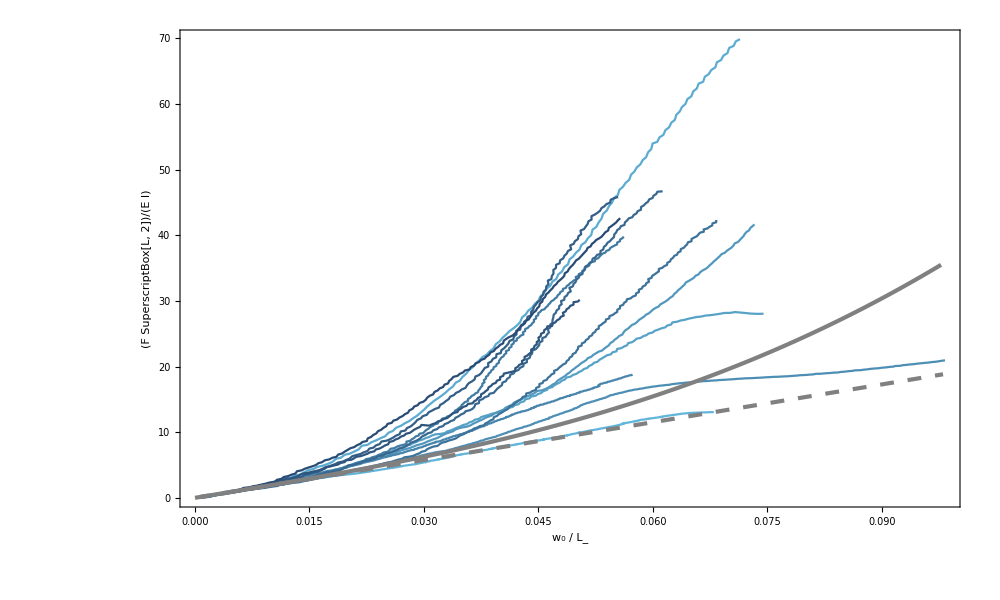

```mathematica
FFplt=Show[
ListPlot[dimensionlessFw0,
Joined->True
,PlotStyle->colorlist
,ImageSize->1000
,GridLines->None
,Ticks->Automatic
,AxesStyle->Directive[Black,FontFamily->"Times",40]
,Frame->True
,FrameStyle->Directive[Black,Thick,FontFamily->"Times",28]
,FrameLabel->{Style["w_0 / L_",Black(*,Italic*),FontFamily->"Times",28],Style["(F SuperscriptBox[L, 2])/(E I)",Black,FontFamily->"Times",28]}
,RotateLabel->False,
AspectRatio->0.6],
ListPlot[WKSol[[;;150]],Joined->True,PlotStyle->{Gray,Thickness[0.003]}],
Plot[192x,{x,0,0.098},PlotStyle->{Dashing[0.01],Gray,Thickness[0.003]}]]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/wenqiangfang/Dropbox (Brown)/Apps/Sawtooth_Pattern_PartII Theory/ResearchNote

```mathematica
Export["Figure/FFplt.EPS",FFplt]
```

FFplt.EPS

### Failure Strength of FF

```mathematica
BendTests=Import["data/201708_BendTests_FF_processed_data_Info.mat","MAT"];
Bendlabels=Import["data/201708_BendTests_FF_processed_data_Info.mat","Labels"]
```

{Bstif,D,E,Fstar,K_s,Kc_SE,Kcant,L,N_L,SSpattern,evbool,indx_fail,sD,s_L,w0star,w_sstar}

```mathematica
evbool=Flatten[ BendTests[[Position[Bendlabels,"evbool"][[1,1]] ]]];
Dlist =Pick[Flatten[ BendTests[[Position[Bendlabels,"D"][[1,1]] ]]],evbool];
Fstar =Pick[Flatten[ BendTests[[Position[Bendlabels,"Fstar"][[1,1]] ]]],evbool];
Llist=Pick[Flatten[ BendTests[[Position[Bendlabels,"L"][[1,1]] ]]],evbool];
Ilist = π/4(Dlist/2)^4;
```

```mathematica
FFstrength=(Fstar Llist Dlist/2)/(4  Ilist)
```

{2.81232×10^9,6.26958×10^9,3.90078×10^9,5.32217×10^9,3.01726×10^9,2.37512×10^9,3.80831×10^9,1.09959×10^9,1.08003×10^10,4.54474×10^9,4.69725×10^9,4.88739×10^8}

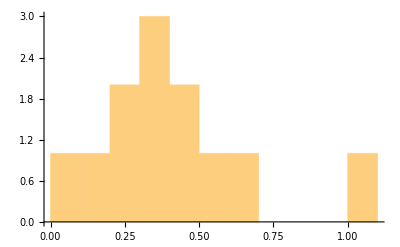

```mathematica
Histogram[FFstrength,10]
```

### Failure Strength of SS

```mathematica
BendTests=Import["data/201708_BendTests_SS_processed_data_Info.mat","MAT"];
Bendlabels=Import["data/201708_BendTests_SS_processed_data_Info.mat","Labels"]
```

{Bstif,D,E,Fslp,Fstar,K_s,Kc_SE,Kcant,L,N_L,SSpattern,axL,dSstar,evbool,indx_fail,indx_slp,sD,s_L,w0slp,w0star,w_sslp,w_sstar}

```mathematica
evbool=Flatten[ BendTests[[Position[Bendlabels,"evbool"][[1,1]] ]]];
Dlist =Pick[Flatten[ BendTests[[Position[Bendlabels,"D"][[1,1]] ]]],evbool];
Fstar =Pick[Flatten[ BendTests[[Position[Bendlabels,"Fstar"][[1,1]] ]]],evbool];
Llist=Pick[Flatten[ BendTests[[Position[Bendlabels,"L"][[1,1]] ]]],evbool];
Ilist = π/4(Dlist/2)^4;
```

```mathematica
SSstrength=(Fstar Llist Dlist/2)/(4  Ilist)
```

{1.00603×10^9,7.84892×10^8,8.93268×10^8,8.31022×10^8,7.20128×10^8,9.53489×10^8,8.62152×10^8,1.14527×10^9,1.1681×10^9,9.11236×10^8,9.20543×10^8,9.27641×10^8,5.82998×10^8,9.08426×10^8,9.97637×10^8,7.74991×10^8,1.02553×10^9,7.63955×10^8,7.79328×10^8,6.75538×10^8,7.8102×10^8,1.29077×10^9,1.07468×10^9,1.11264×10^9,6.70605×10^8,8.15187×10^8,9.57655×10^8,8.69048×10^8,9.30796×10^8,8.4985×10^8,1.16446×10^9,7.84046×10^8,8.49871×10^8,6.27875×10^8,3.17823×10^8,1.01153×10^9,9.69734×10^8,1.06368×10^9}

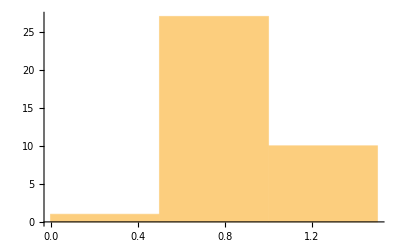

```mathematica
Histogram[SSstrength,3]
```

```mathematica
FFstrength//Max
FFstrength//Min
```

1.08003×10^10

4.88739×10^8

```mathematica
SSstrength//Max
SSstrength//Min
```

1.29077×10^9

3.17823×10^8

```mathematica
Range[0.3,10.9,0.2]
```

{0.3,0.5,0.7,0.9,1.1,1.3,1.5,1.7,1.9,2.1,2.3,2.5,2.7,2.9,3.1,3.3,3.5,3.7,3.9,4.1,4.3,4.5,4.7,4.9,5.1,5.3,5.5,5.7,5.9,6.1,6.3,6.5,6.7,6.9,7.1,7.3,7.5,7.7,7.9,8.1,8.3,8.5,8.7,8.9,9.1,9.3,9.5,9.7,9.9,10.1,10.3,10.5,10.7,10.9}

{{0.3,0.4,0.5,0.6,0.7,0.8,0.9,1,1.5,2,3,4,5,10,15}}

```mathematica
FFstrength/10^9
```

{2.81232,6.26958,3.90078,5.32217,3.01726,2.37512,3.80831,1.09959,10.8003,4.54474,4.69725,0.488739}

```mathematica
Range[0,10,1]
```

{0,1,2,3,4,5,6,7,8,9,10}

```mathematica
RGBColor[{80,99,126}/255]
```

RGBColor[{Rational[16, 51], Rational[33, 85], Rational[42, 85]}]

```mathematica
SSstrength/10^9//Min
```

0.317823

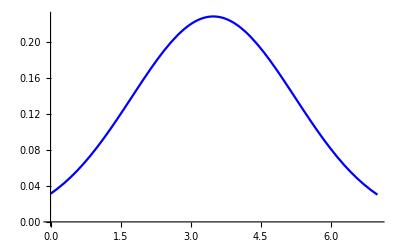

```mathematica
Plot[1 PDF[NormalDistribution[Mean@Select[FFstrength/10^9,#<10&],StandardDeviation@Select[FFstrength/10^9,#<10&]],x],{x,0,7},PlotStyle->Blue]
```

```mathematica
{Mean@Select[FFstrength/10^9,#<10&],StandardDeviation@Select[FFstrength/10^9,#<10&]}
```

{3.48508,1.74843}

```mathematica
{Mean[SSstrength/10^9],StandardDeviation[SSstrength/10^9]}
```

{0.888775,0.185454}

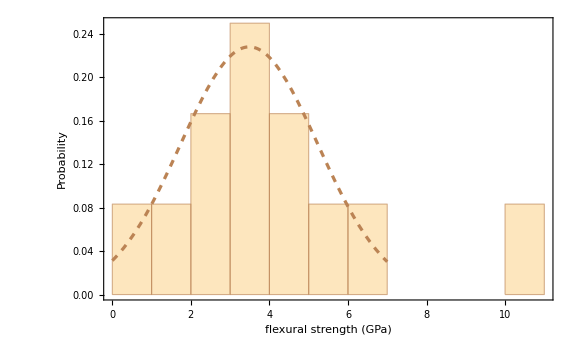

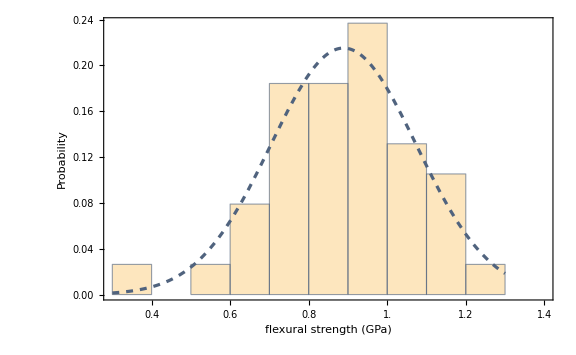

```mathematica
FFFlexural=Show[Histogram[FFstrength/10^9,10,"Probability",ChartStyle->Directive[{
EdgeForm[RGBColor[{187,131,84}/255]]
,FaceForm[Directive[RGBColor[{187,131,84}/255],Opacity[0.5]]]
}],
ImageSize->Large,ImagePadding->{{All,3},{All,3}},
GridLines->None,Axes->False,AxesStyle->Directive[Black,FontFamily->"Times",24],Frame->True,FrameStyle->Directive[FontFamily->"Times",20],
FrameTicks->{{Automatic,None},{Range[0,11],None}},FrameLabel->{Style["flexural strength (GPa)",Black,FontFamily->"Times",24],Style["Probability",Black,FontFamily->"Times",24]},RotateLabel->True
,PlotRange->All],
Plot[1 PDF[NormalDistribution[Mean@Select[FFstrength/10^9,#<10&],StandardDeviation@Select[FFstrength/10^9,#<10&]],x],{x,0,7},PlotStyle->{Dashed,RGBColor[{187,131,84}/255],Thickness[0.004]}]]
bspe={0.30,1.30,0.1};
SSFlexural=Show[Histogram[SSstrength/10^9,bspe,"Probability",ChartStyle->Directive[{
EdgeForm[RGBColor[{80,99,126}/255]]
,FaceForm[Directive[RGBColor[{80,99,126}/255],Opacity[0.5]]]
}],
ImageSize->Large,GridLines->None,Axes->False,AxesStyle->Directive[Black,FontFamily->"Times",24],Frame->True,FrameStyle->Directive[FontFamily->"Times",20],
FrameTicks->{{Automatic,None},{Range[0,1.4,0.1],None}},FrameLabel->{Style["flexural strength (GPa)",Black,FontFamily->"Times",24],Style["Probability",Black,FontFamily->"Times",24]},RotateLabel->True
,PlotRange->{{0.3,1.4},Automatic}],
Plot[0.1 PDF[NormalDistribution[Mean[SSstrength/10^9],StandardDeviation[SSstrength/10^9]],x],{x,0.3,1.3},PlotStyle->{Dashed,RGBColor[{80,99,126}/255],Thickness[0.004]}]]
```

```mathematica
Export["../Figures/FlexuralStrengthFF.EPS",FFFlexural,ImageResolution->500]
```

../Figures/FlexuralStrengthFF.EPS

```mathematica
Export["../Figures/FlexuralStrengthFF.EPS",FFFlexural,ImageResolution->500]
Export["../Figures/FlexuralStrengthSS.EPS",SSFlexural,ImageResolution->500]
```

../Figures/FlexuralStrengthFF.EPS

../Figures/FlexuralStrengthSS.EPS